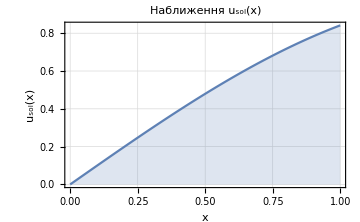
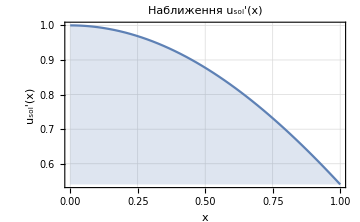

‖u_sol‖_0=0.522184												‖u_sol‖_1=1.

################################################[----FEM n=4 h=1/4 t=1----]################################################

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression 1+i cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at x = 1..

Part::pkspec1: The expression j cannot be used as a part specification.

Part::pkspec1: The expression 1+j cannot be used as a part specification.

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at x = 1..

M=(0.166667 | 0.0416667 | 0. | 0.
0.0416667 | 0.166667 | 0.0416667 | 0.
0. | 0.0416667 | 0.166667 | 0.0416667
0. | 0. | 0.0416667 | 0.0833333)

A=(8. | -4. | 0. | 0.
-4. | 8. | -4. | 0.
0. | -4. | 8. | -4.
0. | 0. | -4. | 4.)

M+Θ*△t*A=(0.206667 | 0.0216667 | 0. | 0.
0.0216667 | 0.206667 | 0.0216667 | 0.
0. | 0.0216667 | 0.206667 | 0.0216667
0. | 0. | 0.0216667 | 0.103333)

F={0.0781425,0.151426,0.215295,0.676872}

q={0.280434,0.541333,0.764375,0.933593}

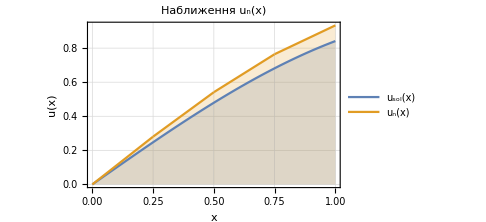
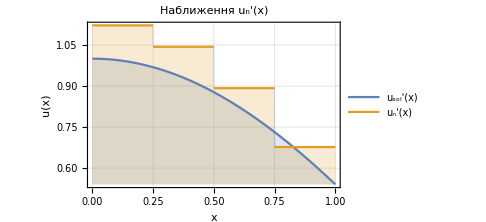

```mathematica
a=0;b=1;
μ[x_]:=1;β[x_]:=0;σ[x_]:=0;
u0 = 0; u1 = Cos[1]; Θ=1/2;
ψ[x_,t_]:=1/(t+1)*Sin[x]; 
uzero[x_]:=Sin[x]+ψ[x,0];
f[x_,t_]:=Sin[x]*(t^2+3*t+1)/(1+t)^2;
Subscript[t, begin]=1;Subscript[t, max]=25;deltat =0.01;
nt = Subscript[t, begin]/deltat;
n = 4;
$MaxPiecewiseCases=700;
(*Точний розвязок диф рівняння*)
Subscript[u, sol][x_]:=Sin[x];
Subscript[plot1u, sol]=Plot[Subscript[u, sol][x],{x,a,b},FrameLabel->{"x ","u_sol(x) "},PlotLabel->Style[Framed["Наближення u_sol(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[plot2u, sol]=Plot[Subscript[u, sol]'[x],{x,a,b},FrameLabel->{"x ","u_sol'(x) "},PlotLabel->Style[Framed["Наближення u_sol'(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[norma1u, sol]=√NIntegrate[Subscript[u, sol][x]^2,{x,a,b}];
Subscript[norma2u, sol]=√NIntegrate[(Subscript[u, sol][x])^2+(Subscript[u, sol]'[x])^2,{x,a,b}];
Print[Subscript[plot1u, sol], "     ", Subscript[plot2u, sol]];
Print["‖u_sol‖_0=",Subscript[norma1u, sol],"\t\t\t\t\t\t\t\t\t\t\t\t‖u_sol‖_1=", Subscript[norma2u, sol]];
(*Функції Куранта*)
ϕ[x0_,i0_] :=
Module[{x=x0, i=i0, k, m},k=i+1; m=i-1;
Piecewise[{
{Piecewise[{{(x-w⟦m⟧)/(w⟦i⟧-w⟦m⟧), w⟦m⟧≤x≤w⟦i⟧},{(w⟦k⟧-x)/(w⟦k⟧-w⟦i⟧),w⟦i⟧≤x≤w⟦k⟧}, {0,x<w⟦i⟧ || x>w⟦k⟧}}],i≠ 1 && i≠n+1}, 
{Piecewise[{{(w⟦k⟧-x)/(w⟦k⟧-w⟦i⟧),w⟦i⟧≤x≤w⟦k⟧},{0,w⟦k⟧<x≤1}}], i==1},
{Piecewise[{{(x-w⟦m⟧)/(w⟦i⟧-w⟦m⟧), w⟦m⟧≤x≤w⟦i⟧},{0,0≤x<w⟦i⟧}}], i==n+1}
}]];
h = (b-a)/n;
w = Table[a+i*h, {i,0,n}];
Print["################################################[----FEM n=",n," h=",h, " t=",Subscript[t, begin],"----]################################################"];
matrixM = 
SparseArray[{{i_,j_}/;Abs[i-j]≤1->
NIntegrate[(ϕ[x,i+1]*ϕ[x,j+1]),
{x,a,b}, Method->"DoubleExponential"]}, {n,n},0.];
matrixA= 
SparseArray[{{i_,j_}/;Abs[i-j]≤1->
NIntegrate[(μ[x]*D[ϕ[x,j+1], x]*D[ϕ[x,i+1], x]+β[x]*D[ϕ[x,j+1], x]*ϕ[x,i+1]+σ[x]*ϕ[x,i+1]*ϕ[x,j+1]),
{x,a,b}, Method->"DoubleExponential"]}, {n,n},0.];
Print["M=",MatrixForm[matrixM]];
Print["A=",MatrixForm[matrixA]];
matrixTotal = matrixM+Θ*deltat*matrixA;
Print["M+Θ*△t*A=",MatrixForm[matrixTotal]];
(*For[k=1,k<=nt,k++,*)
ut1[x_] := ∑_(i=1)^n (u0+deltat*uzero[w⟦i+1⟧])*ϕ[x,i+1];
ut2[x_]:= ∑_(i=1)^n (ut1[w⟦i+1⟧]+deltat*uzero[w⟦i+1⟧])*ϕ[x,i+1];
ut3[x_]:= ∑_(i=1)^n (ut2[w⟦i+1⟧]+deltat*uzero[w⟦i+1⟧])*ϕ[x,i+1];
ut4[x_]:= ∑_(i=1)^n (ut3[w⟦i+1⟧]+deltat*uzero[w⟦i+1⟧])*ϕ[x,i+1];
ut5[x_]:= ∑_(i=1)^n (ut4[w⟦i+1⟧]+deltat*uzero[w⟦i+1⟧])*ϕ[x,i+1];
ut6[x_]:= ∑_(i=1)^n (ut5[w⟦i+1⟧]+deltat*uzero[w⟦i+1⟧])*ϕ[x,i+1];
ut7[x_]:= ∑_(i=1)^n (ut6[w⟦i+1⟧]+deltat*uzero[w⟦i+1⟧])*ϕ[x,i+1];
ut8[x_]:= ∑_(i=1)^n (ut7[w⟦i+1⟧]+deltat*uzero[w⟦i+1⟧])*ϕ[x,i+1];
ut9[x_]:= ∑_(i=1)^n (ut8[w⟦i+1⟧]+deltat*uzero[w⟦i+1⟧])*ϕ[x,i+1];
ut10[x_]:= ∑_(i=1)^n (ut9[w⟦i+1⟧]+deltat*uzero[w⟦i+1⟧])*ϕ[x,i+1];
unext[x_]:=ut2[x];

F = Table[NIntegrate[f[x,Subscript[t, begin]]*ϕ[x,i+1],{x,a,b}]+u1*μ[b]*ϕ[b,i+1]+deltat* NIntegrate[(μ[x]*D[uzero[x], x]*D[ϕ[x,i+1], x]+β[x]*D[unext[x], x]*ϕ[x,i+1]+σ[x]*unext[x]*ϕ[x,i+1]),
{x,a,b}, Method->"DoubleExponential"], {i,1,n}];
Print["F=",F];
q = LinearSolve[matrixA,F];
Print["q=",q];
Subscript[u, n][x_]:=u0+∑_(i=1)^n q[[i]]*ϕ[x,i+1];
difference1 = Plot[{Subscript[u, sol][x], Subscript[u, n][x]}, {x,a,b}, FrameLabel->{"x ","u(x) "},PlotLegends->"Expressions",PlotLabel->Style[Framed["Наближення u_n(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
difference2 = Plot[{Subscript[u, sol]'[x], Subscript[u, n]'[x]}, {x,a,b}, FrameLabel->{"x ","u(x) "},PlotLegends->"Expressions",PlotLabel->Style[Framed["Наближення u_n'(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Print[difference1, "  ", difference2];
```